Practical-1: Bisection Method
Name: Devansh Tyagi
Roll No: 20221416
B.Sc. (Hons.) Computer Science

Bisection Method: For Given Parameters
Ques-1

Your value do not satisfy the IVP, so change the values.

1th iteration value is : 1.

Estimate error in 1th iteration is : 1.

2th iteration value is : 1.5

Estimate error in 2th iteration is : 0.5

3th iteration value is : 1.75

Estimate error in 3th iteration is : 0.25

4th iteration value is : 1.625

Estimate error in 4th iteration is : 0.125

5th iteration value is : 1.5625

Estimate error in 5th iteration is : 0.0625

6th iteration value is : 1.59375

Estimate error in 6th iteration is : 0.03125

7th iteration value is : 1.57813

Estimate error in 7th iteration is : 0.015625

8th iteration value is : 1.57031

Estimate error in 8th iteration is : 0.0078125

9th iteration value is : 1.57422

Estimate error in 9th iteration is : 0.00390625

10th iteration value is : 1.57227

Estimate error in 10th iteration is : 0.00195313

11th iteration value is : 1.57129

Estimate error in 11th iteration is : 0.000976563

12th iteration value is : 1.5708

Estimate error in 12th iteration is : 0.000488281

13th iteration value is : 1.57056

Estimate error in 13th iteration is : 0.000244141

14th iteration value is : 1.57068

Estimate error in 14th iteration is : 0.00012207

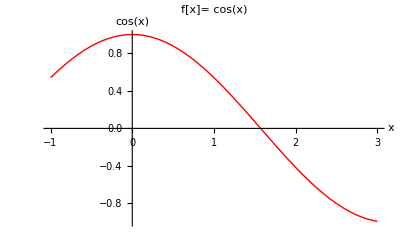

```mathematica
x0 = 0;
x1 = 2.0;
Nmax = 20;
eps = 0.0001;
f[x_] := Cos[x];
IF[N[f[x0]*f[x1]] > 0,
Print["Your value do not satisfy the IVP, so change the values."],
For[i = 1, i<= Nmax, i++, m = (x0 + x1)/2;
	If[Abs[(x1 - x0)/2] < eps, Return[m],
		Print[i, "th iteration value is : ", m];
		Print["Estimate error in ", i, "th iteration is : ", (x1 - x0)/2];
		If[f[m]*f[x1] > 0, x1 = m, x0 = m]
		]
];
Print["Root is : ", m];
Print["Estimated error in ", i, "th iteration is : ", (x1 - x0)/2]];

Plot[f[x], {x, -1, 3}, PlotRange->{-1,1}, PlotStyle->{Red, Thick}, PlotLabel->"f[x]="f[x], AxesLabel->{x, f[x]}]
```

Ques-2

Your value do not satisfy the IVP, so change the values.

1th iteration value is : 1.

Estimate error in 1th iteration is : 1.

2th iteration value is : 0.5

Estimate error in 2th iteration is : 0.5

3th iteration value is : 0.75

Estimate error in 3th iteration is : 0.25

4th iteration value is : 0.625

Estimate error in 4th iteration is : 0.125

5th iteration value is : 0.5625

Estimate error in 5th iteration is : 0.0625

6th iteration value is : 0.53125

Estimate error in 6th iteration is : 0.03125

7th iteration value is : 0.515625

Estimate error in 7th iteration is : 0.015625

8th iteration value is : 0.523438

Estimate error in 8th iteration is : 0.0078125

9th iteration value is : 0.519531

Estimate error in 9th iteration is : 0.00390625

10th iteration value is : 0.517578

Estimate error in 10th iteration is : 0.00195313

11th iteration value is : 0.518555

Estimate error in 11th iteration is : 0.000976563

12th iteration value is : 0.518066

Estimate error in 12th iteration is : 0.000488281

13th iteration value is : 0.517822

Estimate error in 13th iteration is : 0.000244141

14th iteration value is : 0.5177

Estimate error in 14th iteration is : 0.00012207

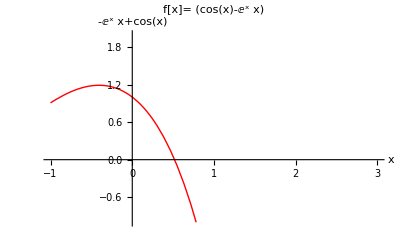

```mathematica
x0 = 0;
x1 = 2.0;
Nmax = 20;
eps = 0.0001;
f[x_] := Cos[x] - x*ⅇ^x;
IF[N[f[x0]*f[x1]] > 0,
Print["Your value do not satisfy the IVP, so change the values."],
For[i = 1, i<= Nmax, i++, m = (x0 + x1)/2;
	If[Abs[(x1 - x0)/2] < eps, Return[m],
		Print[i, "th iteration value is : ", m];
		Print["Estimate error in ", i, "th iteration is : ", (x1 - x0)/2];
		If[f[m]*f[x1] > 0, x1 = m, x0 = m]
		]
];
Print["Root is : ", m];
Print["Estimated error in ", i, "th iteration is : ", (x1 - x0)/2]];

Plot[f[x], {x, -1, 3}, PlotRange->{-1,2}, PlotStyle->{Red, Thick}, PlotLabel->"f[x]="f[x], AxesLabel->{x, f[x]}]
```